# MATHUSLA Detector Calculation

Run this first

### Defining box geometry and functions for computing event yield

Input the parameters of the box here: x is the vertical axis, y is perpendicular to the beam (and horizontal), and z is along the beamline

```mathematica
boxdefinition=boxdefinitionMATHUSLA={{100,120},{-100,100},{100,300}};
```

#### Setting up box definitions and relevant coordinate transformations

```mathematica
θfromη[η_]:=2 ArcCot[ⅇ^η];
ηfromθ[θ_]:=-Log[Tan[θ/2]];
```

Creates a parametric definition f(t,w) ( where t and w run from 0 to 1) of an input plane segment

```mathematica
planesegmentParametricDefinition[currentplanesegment_]:=Module[{twocoordposns,basepoint,corner1,corner2},
twocoordposns=Position[currentplanesegment,x_/;Length[x]==2]//Flatten;
basepoint={If[Length[currentplanesegment[[1]]]==2,currentplanesegment[[1]][[1]],currentplanesegment[[1]]],
If[Length[currentplanesegment[[2]]]==2,currentplanesegment[[2]][[1]],currentplanesegment[[2]]],
If[Length[currentplanesegment[[3]]]==2,currentplanesegment[[3]][[1]],currentplanesegment[[3]]]};
corner1=basepoint;
corner1[[twocoordposns[[1]]]]=currentplanesegment[[twocoordposns[[1]]]][[2]];
corner2=basepoint;
corner2[[twocoordposns[[2]]]]=currentplanesegment[[twocoordposns[[2]]]][[2]];
basepoint + t (corner1-basepoint) + w (corner2 - basepoint)
]
(*Outputs 6 plane segments for a box defined by its x, y, and z ranges*) 
planesegmentsfromboxdefinition[boxdefinition_]:={
{boxdefinition[[1]],boxdefinition[[2]],boxdefinition[[3]][[1]]}
,
{boxdefinition[[1]],boxdefinition[[2]],boxdefinition[[3]][[2]]}
,
{boxdefinition[[1]],boxdefinition[[2]][[1]],boxdefinition[[3]]}
,
{boxdefinition[[1]],boxdefinition[[2]][[2]],boxdefinition[[3]]}
,
{boxdefinition[[1]][[1]],boxdefinition[[2]],boxdefinition[[3]]}
,
{boxdefinition[[1]][[2]],boxdefinition[[2]],boxdefinition[[3]]}
}
```

## Set up particle path geometry

```mathematica
beamaxis={0,0,0}+s{0,0,1};
```

{{s→208.583,t→0.5,w→0.415244},{s→250.3,t→0.5,w→0.598293}}

{{100.,0.,183.049},{120.,0.,219.659}}

{208.583,250.3}

-Graphics3D-

estimate geometric coverage

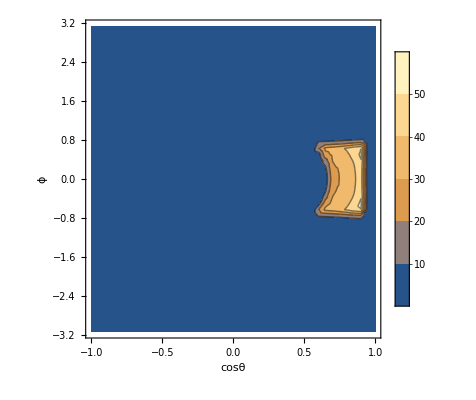

fraction of solid angle covered:

0.036

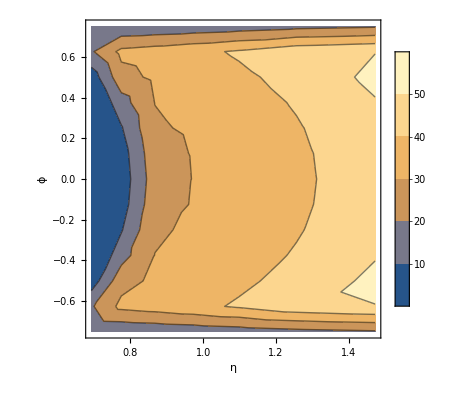

0.672102

```mathematica
(*This sets the trajectory of the particle of interest that originates at the interaction point*)
{lineθ,lineϕ}={0.5,0};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

(*This determines the intersections of a particle trajectory (currentline) and a detector determined by boxdfinition *)
intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 ) && (s/.#)≥0&] (*The conditions ensure only physical solutions are kept*)

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(intersectionpoints[[1]].intersectionpoints[[1]]),√(intersectionpoints[[2]].intersectionpoints[[2]])}

Show[
ParametricPlot3D[{
Evaluate[planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]]
},{t,0,1},{w,0,1},
PlotRange->{{-1,1},{-1,1},{-1,1}}300,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,0,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ParametricPlot3D[beamaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ListPointPlot3D[intersectionpoints,PlotStyle->{Red,PointSize[0.02]}]
]



"estimate geometric coverage"
L2mL1asfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(intersectionpoints[[2]].intersectionpoints[[2]])-√(intersectionpoints[[1]].intersectionpoints[[1]])
}
,{cosθ,1,-1,-0.05},{ϕ,-π,π,2π/50}],1];

ListContourPlot[L2mL1asfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]


"fraction of solid angle covered:"
1/(4π)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)


ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1asfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]


(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//ηfromθ[Min[#]]-ηfromθ[Max[#]]&)(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)
```

## Define particle entry and exit points and setting up event yield

```mathematica
DecayProb[L1_?NumericQ,L2_?NumericQ,bλ_?NumericQ]:=ⅇ^(-L1/bλ)-ⅇ^(-L2/bλ);
```

BoxDetectorL1L2m takes in the box definition and defining variables of a a particle trajectory, θ and ϕ. From these, it determines the intercept points L1 and L2 and outputs their radial distance from the interaction point. Trajectories with no intersection return complex values.

```mathematica
BoxDetectorL1L2m[θ_,ϕ_,boxdefinition_]:=Module[{cosθ},
cosθ=Cos[θ];
{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

{√(intersectionpoints[[1]].intersectionpoints[[1]]),√(intersectionpoints[[2]].intersectionpoints[[2]])}
];
```

As the name implies, this function determines the values of Cos θ and ϕ that lead to trajectories that reach the detector. The interior table creates a list of values for each angular coordinate pair that has the form {Cos θ, ϕ, distance travelled in the detector}. If the angular coordinates do not lead to an intersecting trajectory, the value of the third entry is set to 0. The final several lines convert this information into a range of angular values {Cos θ min, Cos θ max}, {ϕ min, ϕ max} while making certain that we don’t extend beyond the coordinate limits due to the addition of the variable steps.

```mathematica
Findcosθϕrange[boxdefinition_,cosθstep_:2/20,ϕstep_:2π/20]:=Module[{},

L2mL1asfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionsolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,t,w}]&/@(planesegmentParametricDefinition[#]&/@planesegmentsfromboxdefinition[boxdefinition]),1]
,(0≤ (t/.#)≤ 1) && (0≤ (w/.#)≤ 1 )&& (s/.#)≥0&];

intersectionpoints=If[Length[intersectionsolutions]>0,
Sort[currentline/.intersectionsolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

√(intersectionpoints[[2]].intersectionpoints[[2]])-√(intersectionpoints[[1]].intersectionpoints[[1]])
}
,{cosθ,1,-1,-cosθstep},{ϕ,-π,π,ϕstep}],1];


preRange={(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[1]]//{Min[#]-cosθstep,Max[#]+cosθstep}&)
,(Transpose[Select[L2mL1asfncosθϕ,#[[3]]>0&]][[2]]//{Min[#]-ϕstep,Max[#]+ϕstep}&)
};

range ={{If[preRange[[1]][[1]]<-1,-1,preRange[[1]][[1]]],If[preRange[[1]][[2]]>1,1,preRange[[1]][[2]]]},{If[preRange[[2]][[1]]<-Pi,-Pi,preRange[[2]][[1]]],If[preRange[[2]][[2]]>Pi,Pi,preRange[[2]][[2]]]}}

];
```

```mathematica
ComputeDecayEfficiencyBoxDetector[θblist_, currentcτmeters_, boxdefinition_,currentcosθϕrange_]:=Module[{θblistflat},
θblistflat=Flatten[θblist,1];
(*we choose ϕ randomly to lie within the range covered by the box detector, and weigh accordingly*)
(*(this would obviously not be ok if we wanted to detect two particles per event, since the ϕ correlations have been thrown out, but doesn't matter for us)*)
(currentcosθϕrange[[2]][[2]]-currentcosθϕrange[[2]][[1]])/(2π)( Sum[
X1=θblistflat[[i]];
PX1inBox=(DecayProb[#1⟦1⟧,#1⟦2⟧,currentcτmeters X1⟦2⟧]&)[BoxDetectorL1L2m[X1⟦1⟧,RandomReal[currentcosθϕrange[[2]]],boxdefinition]];
{PX1inBox,PX1inBox^2}
,{i,1,Length[θblistflat]}]
//{#[[1]],√(#[[2]])}&
)/Length[θblist]//Re
]
```

From the below  functions, it appears that the .dat files are organized in scattering events that have a certain number dark pions (points). The three terms of the points within each entry are θ, ϕ, and the boost factor (I think).

```mathematica
SetDirectory[NotebookDirectory[]<>"/PythiaSims"]
(* 
Beam energy = 13 TeV
Cross sections from 
https://twiki.cern.ch/twiki/bin/view/LHCPhysics/SUSYCrossSections13TeVstopsbottom
use number of dark colours = 3, cross section scales linearly with Ncd 
*)
(*LLPxsecfb[1750]=3*43.; (*cross section associated with data set*)
LLPxsecfb[1400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10750]=3*43.; (*cross section associated with data set*)*)
LLPxsecfb[11000]=3*6.2; (*cross section associated with data set*)
LLPxsecfb[11500]=3*0.25; (*cross section associated with data set*)

θϕbList[1100]=ReadList["EJ1_1000.dat"][[1]];  (*data*)
θϕbList[4100]=ReadList["EJ4_1000.dat"][[1]];  (*data*)
θϕbList[8100]=ReadList["EJ8_1000.dat"][[1]];  (*data*)
θϕbList[1150]=ReadList["EJ1_1500.dat"][[1]];  (*data*)
θϕbList[4150]=ReadList["EJ4_1500.dat"][[1]];  (*data*)
θϕbList[8150]=ReadList["EJ8_1500.dat"][[1]];  (*data*)
fileIDlist={1100,4100,8100,1150,4150,8150}; (*list of labels of all data set. Will be looped over later.*)

Lumiifb=3000;

(*This routine computes the point of entry and exit for each particle, along the line of motion.*)
L1L2[event_]:=
Table[
BoxDetectorL1L2m[point[[1]],point[[2]],boxdefinition]~Join~{point[[3]]}
,{point,event}];
```

/Users/dylanlinthorne/Dropbox/New Detectors/PythiaSims

```mathematica
(*This routine computes the probability of at least one and at least 2 vertices in MATHUSLHA. The inputs is are the list of (entrypoint,exitpoints) for each event, obtained with the previous routine, as well as the lifetime.*)
EventProb[event_,logcτ_]:=(Module[{problist},
problist=Re[DecayProb[#[[1]],#[[2]],#[[3]]*10^logcτ]]&/@event;
{1-(Times@@(1-problist)),
1-(Times@@(1-problist))-Sum[Times@@(ReplacePart[#,i->1-#[[i]]]&@(1-problist)),{i,Length[problist]}]}
])
```

### Parallel Calculation of Efficiency and Variance

```mathematica
SetDirectory[NotebookDirectory[]<>"/EJData"]
```

/Users/dylanlinthorne/Dropbox/New Detectors/EJData

```mathematica
log10cτlist={-1,-.75,-.5,-.25,0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,3,3.5,4,4.5,7};
Do[
nevents=Length[θϕbList[ID]];
L1L2list=ParallelMap[L1L2,θϕbList[ID]];

efflist[ID]=ParallelTable[{logτ}~Join~Mean[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

variancelist[ID]=ParallelTable[{logτ}~Join~Variance[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

Export["mat_efflist_"<>ToString[ID]<>".txt",efflist[ID],"Table"];Export["mat_varlist_"<>ToString[ID]<>".txt",variancelist[ID],"Table"];

,{ID,fileIDlist}]
```

General::munfl: Exp[-907.268] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1088.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-814.015] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-789.836] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-900.108] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.994] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-907.268] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1088.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-814.015] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-789.836] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-900.108] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.994] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-829.415] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-934.607] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1121.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-829.415] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-934.607] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1121.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1174.71] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1294.27] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3791.71] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1174.71] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1294.27] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3791.71] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1359.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1488.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1575.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1359.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1488.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1575.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1343.95] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1612.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.962] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1343.95] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1612.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.962] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-716.671] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-845.657] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1014.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1062.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1274.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.943] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-716.671] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-845.657] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1014.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1062.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1274.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.943] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.